# Projekt

## Pridobivanje podatkov

Podatke bom vzel iz Wolfram data repository.

```mathematica
podatki = ResourceData["Child Mortality from Malaria"];
```

## Prikaz podatkov nekaterih držav v Afriki, Aziji in Južni Ameriki

Naslednje države sem si izbral, saj so to bile po podatkih dobljenih predvsem na spletnih straneh organizacije WHO države z največjo umrljivostjo po kontinentih.

### Afrika

Te države sem si izbral, saj se tam zgodi skoraj 50% vseh smrtnih primerov zaradi malarije na svetovni ravni.

```mathematica
drzaveAfrika = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAfrikaVrstice=Select[podatki,MemberQ[ drzaveAfrika,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 27 dni ter 0 - 4 let.

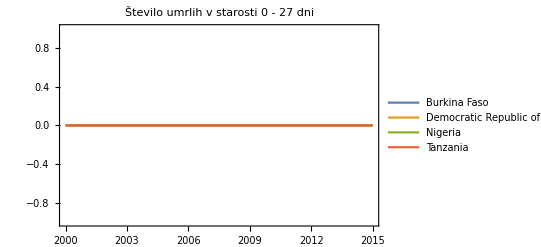

```mathematica
DateListPlot[#["Aged0To27Days"]&/@drzaveAfrikaVrstice,PlotLegends->Table[drzaveAfrikaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 27 dni"]
```

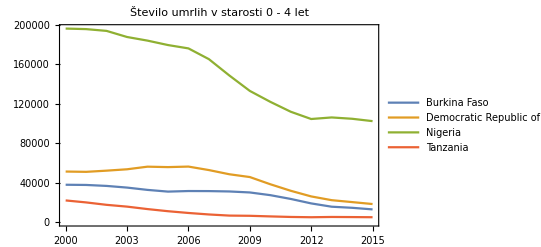

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAfrikaVrstice,PlotLegends->Table[drzaveAfrikaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 4 let"]
```

### Azija

```mathematica
drzaveAzija = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAzijaVrstice=Select[podatki,MemberQ[ drzaveAzija,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 4 let .

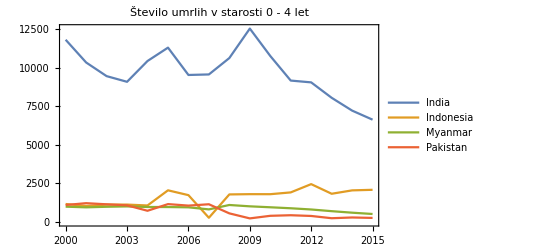

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAzijaVrstice,PlotLegends->Table[drzaveAzijaVrstice[[x]]["Country"],{x,1,4}],PlotLabel->"Število umrlih v starosti 0 - 4 let"]
```

### Južna Amerika in Karibi

```mathematica
drzaveAmerika = {LinguisticAssistant,LinguisticAssistant,LinguisticAssistant,LinguisticAssistant};
drzaveAmerikaVrstice=Select[podatki,MemberQ[ drzaveAmerika,#["Country"]]&];
```

Prikaz števila smrtnih primerov za otroke v starostnem razponu 0 - 4 let .

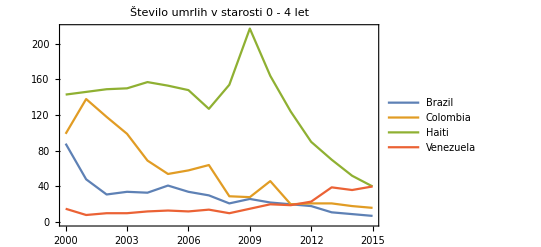

```mathematica
DateListPlot[#["Aged0To4Years"]&/@drzaveAmerikaVrstice,PlotLegends->Table[drzaveAmerikaVrstice[[x]]["Country"],{x,1,4}], PlotLabel->"Število umrlih v starosti 0 - 4 let"]
```

## Prikaz stanja v državah v časovnem obdobju 10 let

### Afrika

```mathematica
VseDrzaveAfrike = EntityList[EntityClass["Country","Africa"]];
```

```mathematica
PodatkiCelotnaAfrika = Select[podatki,MemberQ[VseDrzaveAfrike, #["Country"]]&];
```

#### Prikaz za leto 2005

```mathematica
GeoRegionValuePlot[Table[PodatkiCelotnaAfrika[[x]]["Country"]->PodatkiCelotnaAfrika[[x]]["Aged0To4Years"]["2005"]/PodatkiCelotnaAfrika[[x]]["Country"]["Population"],{x,Length[PodatkiCelotnaAfrika]}]]
```

-Graphics-

#### prikaz za leto 2015

```mathematica
GeoRegionValuePlot[Table[PodatkiCelotnaAfrika[[x]]["Country"]->PodatkiCelotnaAfrika[[x]]["Aged0To4Years"]["2015"]/PodatkiCelotnaAfrika[[x]]["Country"]["Population"],{x,Length[PodatkiCelotnaAfrika]}]]
```

-Graphics-

### Azija

```mathematica
VseDrzaveAzija = EntityList[EntityClass["Country","Asia"]];
```

```mathematica
PodatkiCelotnaAzija = Select[podatki,MemberQ[drzaveAzija, #["Country"]]&];
```

#### Leto 2005

```mathematica
GeoRegionValuePlot[Table[PodatkiCelotnaAzija[[x]]["Country"]->PodatkiCelotnaAzija[[x]]["Aged0To4Years"]["2005"]/PodatkiCelotnaAzija[[x]]["Country"]["Population"],{x,Length[PodatkiCelotnaAzija]}]]
```

-Graphics-

#### Leto 2015

```mathematica
GeoRegionValuePlot[Table[PodatkiAzija[[x]]["Country"]->PodatkiAzija[[x]]["Aged0To4Years"]["2015"]/PodatkiAzija[[x]]["Country"]["Population"],{x,Length[PodatkiAzija]}]]
```

-Graphics-

## Podrobnejsi podatki za drzavo in leto po lastni izbiri

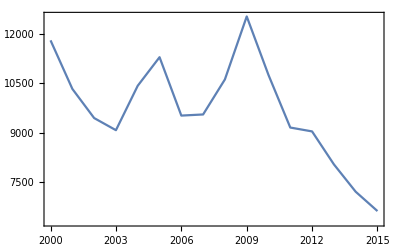

```mathematica
drzava = Entity["Country",InputString["Katero drzavo zelis podrobneje pogledati"]];
leto= InputString["Katero leto te zanima(2001-2014): "];
PridobiPodatke= Select[podatki, #["Country"]==drzava&][[1]]["Aged1To59Months"];
DateListPlot[PridobiPodatke]
```

```mathematica
DateListPlot[PridobiPodatke]
```

-Graphics-

```mathematica
Razlika2005= Normal[PridobiPodatke["2000"]- PridobiPodatke[leto]]
Razlika2015 = Normal[PridobiPodatke["2015"]- PridobiPodatke[leto]]
```

3755

-1414

```mathematica
StringForm["Med letoma 2000 in `` je razlika `` umrljih ljudi med letoma 2015 in `` pa ``.",leto,Razlika2005,leto,Razlika2015]
```

Med letoma 2000 in 2013 je razlika 3755 umrljih ljudi med letoma 2015 in 2013 pa -1414.